## Construcción de tablas

Se han visto ya algunas maneras de formar listas en Wolfram Language. Se puede simplemente escribirlas manualmente. Se puede utilizar Range. Se pueden usar funciones tales como IntegerDigits. Pero una manera muy común y flexible para formarlas es mediante el uso de la función Table.

En su forma más simple,Table construye una lista con el mismo elemento repetido un número especificado de veces.

Forme una lista que tenga el 5 repetido 10 veces:

```mathematica
Table[5,10]
```

{5,5,5,5,5,5,5,5,5,5}

Esto construye una lista con x repetido 10 veces:

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

También se pueden repetir listas:

```mathematica
Table[{1,2},10]
```

{{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2}}

Y, de hecho, cualquier otra cosa; a continuación aparece una lista de 3 gráficos circulares idénticas:

```mathematica
Table[PieChart[{1,1,1}],3]
```

{-Graphics-,-Graphics-,-Graphics-}

Pero, ¿y si se deseara formar una tabla cuyos elementos no sean idénticos? Esto se logra introduciendo una variable, para usarla haciendo una iteración sobre ella.

Itere sobre n para formar una lista donde n tome valores hasta el 5:

```mathematica
Table[a[n],{n,5}]
```

{a[1],a[2],a[3],a[4],a[5]}

Esto funciona de la siguiente manera. Para formar el primer elemento de la lista, se toma n igual a 1, así que a[n] es a[1]. Para el segundo elemento, se toma n igual a 2, así que a[n] es a[2], etc. A n se le llama variable porque cambia de valor a medida que se van construyendo los diferentes elementos de la lista.

Construya una tabla que produzca el valor de n + 1 cuando n toma valores del 1 al 10:

```mathematica
Table[n+1,{n,10}]
```

{2,3,4,5,6,7,8,9,10,11}

Forme una tabla de los 10 primeros cuadrados:

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Con Table se pueden formar tablas de cosas cualesquiera.

He aquí una tabla de listas sucesivamente más grandes, producidas con Range:

```mathematica
Table[Range[n],{n,5}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

Aquí se muestra, en una columna, cada una de las listas producidas anteriormente:

```mathematica
Table[Column[Range[n]],{n,8}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

Ahora se muestra una tabla de gráficos de listas sucesivamente más grandes:

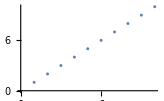
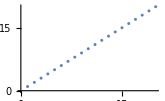
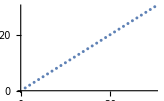

```mathematica
Table[ListPlot[Range[10*n]],{n,3}]
```

Aquí aparecen gráficos circulares con un número de sectores cada vez mayor :

```mathematica
Table[PieChart[Table[1,n]],{n,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Hasta ahora se ha venido usando n como nombre de la variable utilizada, que es algo muy habitual. Pero puede utilizarse para eso cualquier letra minúscula que se desee, o cualquier combinación de letras. Lo importante es que siempre se use el mismo nombre dondequiera que aparezca la variable en cuestión.

expt es un nombre perfectamente adecuado para una variable:

```mathematica
Table[2^expt,{expt,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

Abajo se usa x como nombre de la variable y aparece en varios lugares:

```mathematica
Table[{x,x+1,x^2},{x,5}]
```

{{1,2,1},{2,3,4},{3,4,9},{4,5,16},{5,6,25}}

En Table[f[n],{n,5}], n toma los valores 1, 2, 3, 4, 5. En cambio, Table[f[n],{n,3,5}] indica que hay que comenzar en 3: 3, 4, 5.

Esto genera una tabla donde n varía del 1 al 10:

```mathematica
Table[f[n],{n,10}]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

Esto produce una tabla donde n varía del 4 al 10:

```mathematica
Table[f[n],{n,4,10}]
```

{f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

Aquí se indica que la n debe recorrer los valores del 4 al 10, de 2 en 2:

```mathematica
Table[f[n],{n,4,10,2}]
```

{f[4],f[6],f[8],f[10]}

Wolfram Language hace hincapié en la consistencia así que, por ejemplo, Range actúa igual que Table en lo que se refiere a valores iniciales e incrementos.

Genere la secuencia de números del 4 al 10:

```mathematica
Range[4,10]
```

{4,5,6,7,8,9,10}

Genere la secuencia de números del 4 al 10, de 2 en 2:

```mathematica
Range[4,10,2]
```

{4,6,8,10}

Vaya del 0 al 1 en incrementos de 0.1:

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

Suele haber varias maneras de hacer la misma cosa en Wolfram Language. Así, por ejemplo, se muestra cómo Table y Range pueden producir gráficos idénticos.

Genere una lista y represéntela gráficamente:

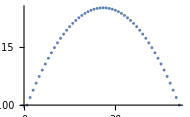

```mathematica
ListPlot[Table[x-x^2,{x,0,1,.02}]]
```

Se obtiene el mismo resultado haciendo algo de aritmética con la secuencia de valores:

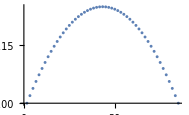

```mathematica
ListPlot[Range[0,1,.02]-Range[0,1,.02]^2]
```

Table siempre calcula por separado cada elemento de la lista que genera, y esto puede observarse al utilizar RandomInteger dentro de Table.

Esto genera 20 enteros aleatorios independientes entre 0 y 10:

```mathematica
Table[RandomInteger[10],20]
```

{3,1,4,3,6,7,6,10,9,2,1,4,5,8,3,8,3,8,3,0}

De hecho, esta lista podría generarse directamente con  RandomInteger.

Otra forma de generar 20 enteros aleatorios entre 0 y 10:

```mathematica
RandomInteger[10,20]
```

{3,0,3,1,9,6,0,8,5,2,7,8,0,10,4,4,9,5,7,1}

Vocabulario

Table[x,5] |   | lista de 5 copias de x
Table[f[n],{n,10}] |   | lista de valores de f[n] donde n varía hasta el 10
Table[f[n],{n,2,10}] |   | lista de valores donde n varía desde el 2 hasta el 10 
Table[f[n],{n,2,10,4}] |   | lista de valores donde n varía del 2 hasta el 10, de 4 en 4 
Range[5,10] |   | lista de los números del 5 al 10
Range[10,20,2] |   | lista de los números del 10 al 20, de 2 en 2
RandomInteger[10,20] |   | lista de 20 enteros aleatorios entre 0 y 10

"10 Exercises Available"
"with 11 extras" | "Get Started »"

Forme una lista con el número 1000 repetido 5 veces. »

| Expected output: |  
  | {1000,1000,1000,1000,1000} |

Cree una lista de los valores de n^3 donde n va del 10 al 20. »

| Expected output: |  
  | {1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000} |

Construya un gráfico con los 20 primeros cuadrados sobre la recta numérica. »

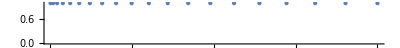
| Expected output: |  
  | -Graphics- |

Construya una lista de los números pares (2, 4, 6, ...) hasta el 20. »

| Expected output: |  
  | {2,4,6,8,10,12,14,16,18,20} |

Use Table para obtener el mismo resultado que Range[10]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10} |

Construya un diagrama de barras de los 10 primeros cuadrados. »

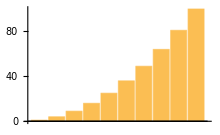
| Expected output: |  
  | -Graphics- |

Forme una tabla de listas de los dígitos de los 10 primeros cuadrados. »

| Expected output: |  
  | {{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}} |

Construya el gráfico, con los puntos unidos, de la longitud de la secuencia de los dígitos de cada uno de los 100 primeros cuadrados. »

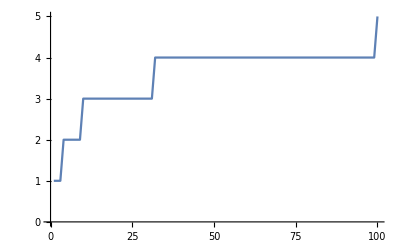
| Expected output: |  
  | -Graphics- |

Forme una tabla del primer dígito de cada uno de los 20 primeros cuadrados. »

| Expected output: |  
  | {1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4} |

Haga el gráfico de los primeros dígitos de los 100 primeros cuadrados. »

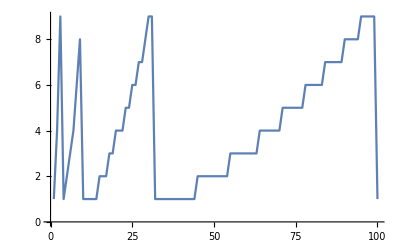
| Expected output: |  
  | -Graphics- |

Forme una lista de las diferencias entre n^3 y n^2 para n menor o igual a 10. »

| Expected output: |  
  | {0,4,18,48,100,180,294,448,648,900} |

Forme una lista de los números impares (1, 3, 5, ...) hasta el 100. »

| Expected output: |  
  | {1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99} |

Cree una lista de los cuadrados de los números pares hasta el 100. »

| Expected output: |  
  | {4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000} |

Cree la lista {-3,-2,-1,0,1,2} utilizando Range. »

| Expected output: |  
  | {-3,-2,-1,0,1,2} |

Construya una lista con los números n hasta el 20, donde cada elemento sea una columna de los valores de n, n^2 y n^3. »

| Expected output: |  
  | {1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000} |

Presente un gráfico, con los puntos unidos, del último dígito de cada uno de los 100 primeros cuadrados. »

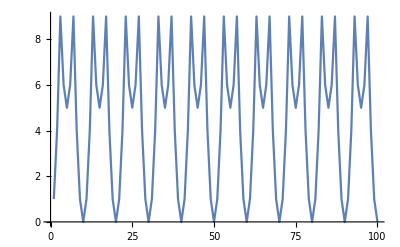
| Expected output: |  
  | -Graphics- |

Cree un gráfico, con los puntos unidos, del primer dígito de cada uno de los primeros 100 múltiplos de 3. »

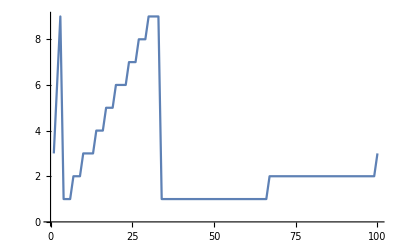
| Expected output: |  
  | -Graphics- |

Produzca un gráfico, con los puntos unidos, de la suma de los dígitos de cada número hasta el 200. »

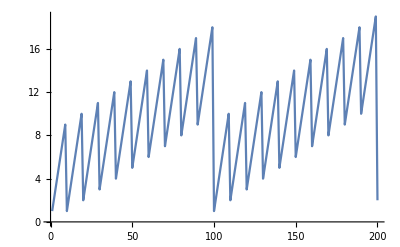
| Expected output: |  
  | -Graphics- |

Construya una gráfica, con los puntos unidos, de la suma de los dígitos para cada uno de los 100 primeros cuadrados. »

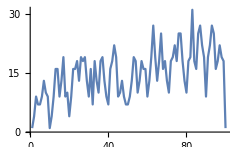
| Expected output: |  
  | -Graphics- |

Obtenga un gráfico, con los puntos sobre la recta numérica, de los números 1/n, con n variando de 1 a 20. »

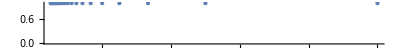
| Expected output: |  
  | -Graphics- |

Produzca un gráfico, con los puntos unidos, de una lista de enteros aleatorios, donde el n-ésimo entero esté entre 0 y n. »

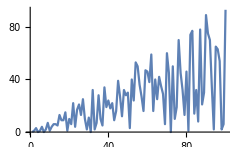
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Qué significa la lista {...} (lista) en Table[n^2,{n,5}]?

Una lista siempre es una forma de reunir cosas. En este caso lo que se reúne es la variable n con su secuencia de valores hasta el 5. En Wolfram Language, esta forma de usar una lista se llama especificación del iterador.

¿Por qué es necesaria la lista {...} in Table[n^2,{n,5}]?

Porque de esa manera se puede generalizar fácilmente a los arreglos multidimensionales, como en Table[x^2-y^2,{x,5},{y,5}].

¿Qué restricciones hay para los nombres de variables?

Pueden ser cualquier secuencia de letras y números, pero no pueden comenzar con un número. Además, para evitar confusiones con las funciones nativas de Wolfram Language, no deben comenzar con mayúscula.

¿Por qué hay que poner nombre a una variable, si los nombres no importan?

¡Buena pregunta!  En la Sección 26 se verá cómo evitar el uso del nombre de las variables. Esto es más elegante, aunque un poco más abstracto de lo que hasta ahora se viene haciendo con Table.

¿Puede Range trabajar con números negativos?

Desde luego. Range[-2,2] produce {-2,-1,0,1,2}. Range[2,-2] produce {}, por Range[2,-2,-1] produce {2,1,0,-1,-2}.

Notas técnicas

En el caso de que se especifiquen incrementos que no se ajusten bien al tramo que se haya determinado, Range y Table llegarán hasta donde los lleven los incrementos y, potencialmente, se detendrán antes del límite superior. (Así Range[1,6,2] produce {1,3,5}, deteniéndose en 5, y no en 6.)

Usar una forma tal como Table[x,20] requiere tener activa, cuando menos, la Versión 10.2 de Wolfram Language. En versiones anteriores esto tendría que especificarse comoTable[x,{20}].

Para explorar más

La función Table en Wolfram Language »